## Generating Multipoles

### Method One

The first method is to plot the SphericalHarmonicY in Cartesian coordinate system and then transform it using Mollweide method.

```mathematica
plt[l_,m_]:=DensityPlot[Re[SphericalHarmonicY[l,m,θ,ϕ]],{ϕ,-π,π},{θ,0,π},ColorFunction->"TemperatureMap",AspectRatio->0.5,Frame->False]
```

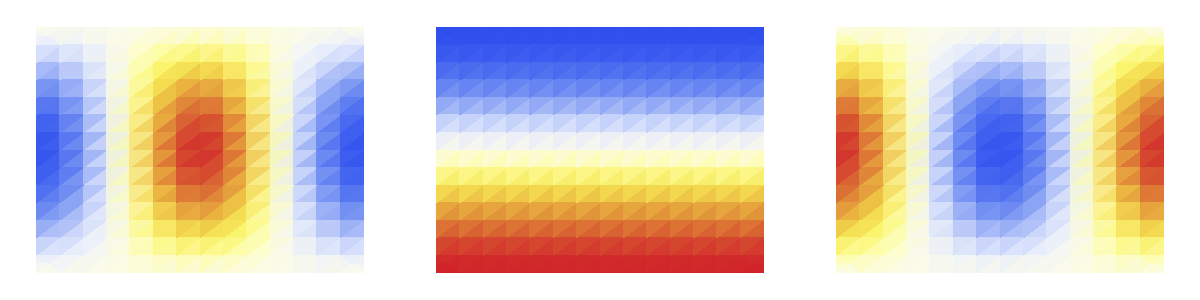

```mathematica
Grid[{grid1=Table[plt[1,m],{m,-1,1}]}]
```

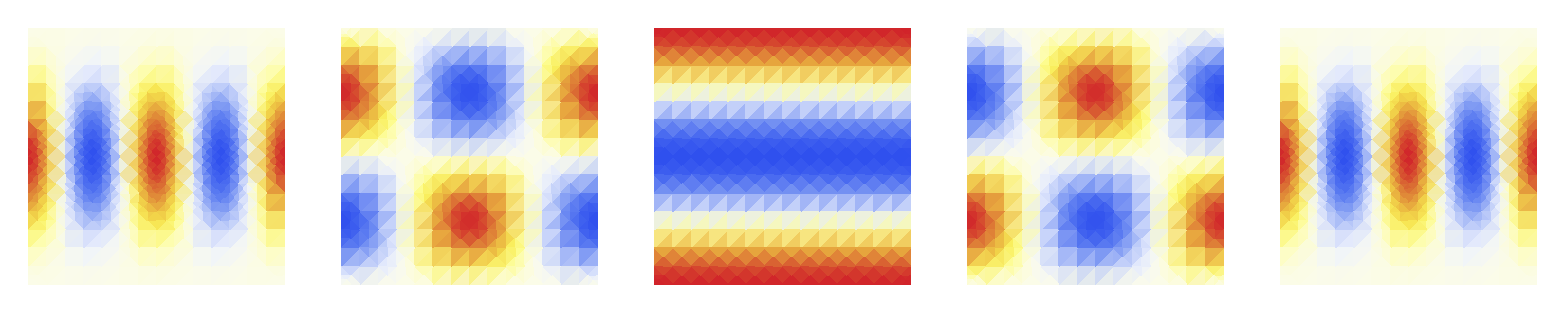

```mathematica
Grid[{grid2=Table[plt[2,m],{m,-2,2}]}]
```

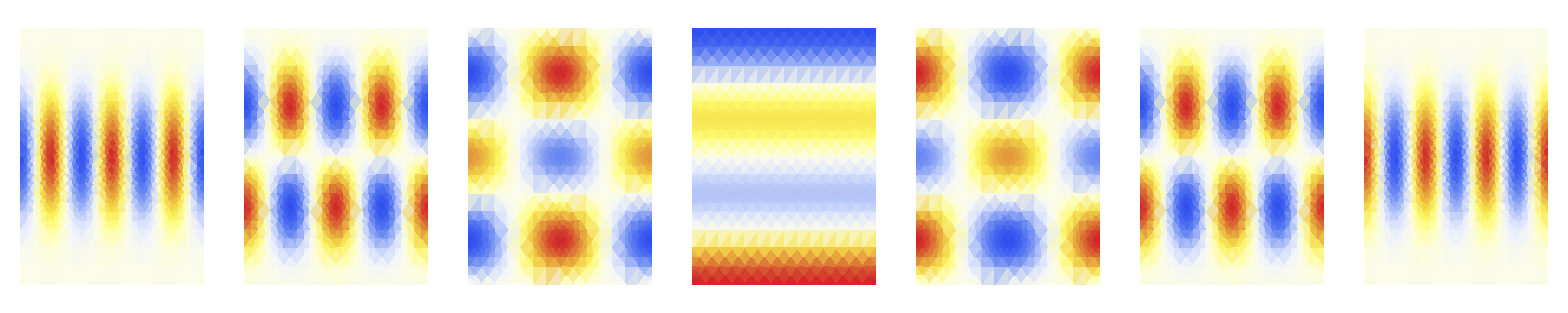

```mathematica
Grid[{grid3=Table[plt[3,m],{m,-3,3}]}]
```

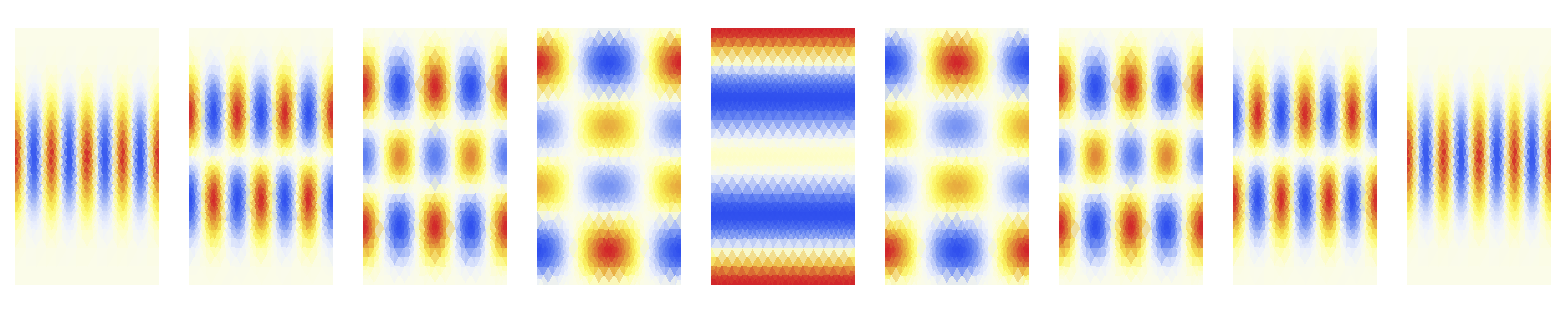

```mathematica
Grid[{grid4=Table[plt[4,m],{m,-4,4}]}]
```

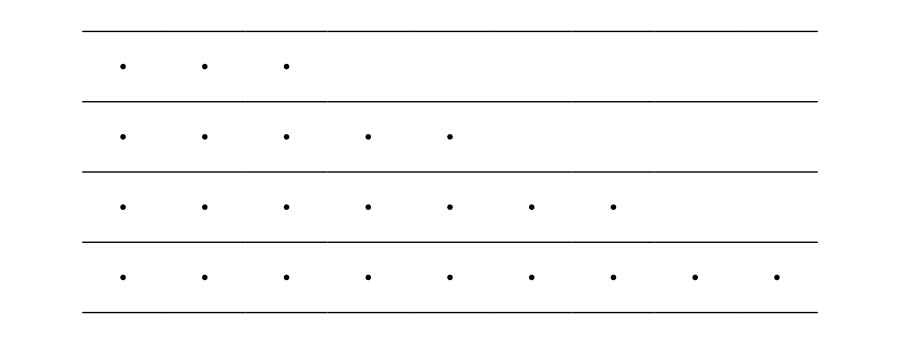

```mathematica
GraphicsGrid[{grid1,grid2,grid3,grid4},Dividers->{False,All},ImageSize->900,Spacings->{Scaled[0.05],Scaled[1]}]
```

```mathematica
invmollweide[{x_,y_}]:=With[{θt=ArcSin[y/(√2)]},{Pi x/(2 √2 Cos[θt]),π/2-ArcSin[(2 θt+Sin[2 θt])/Pi]}]
```

```mathematica
func[img_]:=ImageTransformation[img,invmollweide,DataRange->{{-π,π},{0,π}},PlotRange->{{-3,3},{-1.6,1.6}},Padding->White]
```

```mathematica
grid={func/@Flatten[grid1],func/@Flatten[grid2],func/@Flatten[grid3],func/@Flatten[grid4]};
```

```mathematica
GraphicsGrid[grid,Dividers->{False,All},ImageSize->900]
```

-Graphics-

#### Some Notes on this method

Mollweide Projection

```mathematica
Sin[2 π/2]+2 π/2==π Sin[π/2-0]
```

True

```mathematica
FindRoot[Sin[2θt]+2θt==π Sin[π/2-0],{θt,0}]
FindRoot[Sin[2θt]+2θt==π Sin[π/2-π/2],{θt,0}]
FindRoot[Sin[2θt]+2θt==π Sin[π/2-π],{θt,0}]
FindRoot[Sin[2θt]+2θt==π Sin[π/2-0.95π],{θt,0}]
```

{θt→1.57079}

{θt→0.}

{θt→-1.57079}

{θt→-1.26157}

Thus we have θ=0, θt=π/2, y=√2, x=; θ=π/2  θt=0, y=0,   θ=π  θt=-π/2, y=-√2.

```mathematica
{√2 Sin[π/2],√2 Sin[0],√2 Sin[-π/2]}
```

{√2,0,-√2}

```mathematica
x==(2 √2)/π λ Cos[θt]
```

x==(2 √2 λ Cos[θt])/π

```mathematica
y==√2 Sin[θt]
```

y==√2 Sin[θt]

```mathematica
2θt+Sin[2θt]==π Sin[ϕt]
```

2 θt+Sin[2 θt]==π Sin[ϕt]

```mathematica
ϕt==π/2-θ
```

ϕt==π/2-θ

```mathematica
ψ==λ
```

ψ==λ

```mathematica
invmollweide[{x_,y_}]:=With[{theta=ArcSin[y]},{Pi x/(2 Cos[theta]),ArcSin[(2 theta+Sin[2 theta])/Pi]}]
```

### Method Two

Transform the coordinate first, then plot.

```mathematica
cart[{lambda_,phi_}]:=With[{thetat=fc[phi]},{π/2-2√2/Pi*lambda Cos[thetat],Sin[thetat]}]
fc[phi_]:=Block[{thetat},If[Abs[phi]==Pi/2,phi,thetat/.FindRoot[2 thetat+Sin[2 thetat]==Pi Sin[phi],{thetat,phi}]]];
```

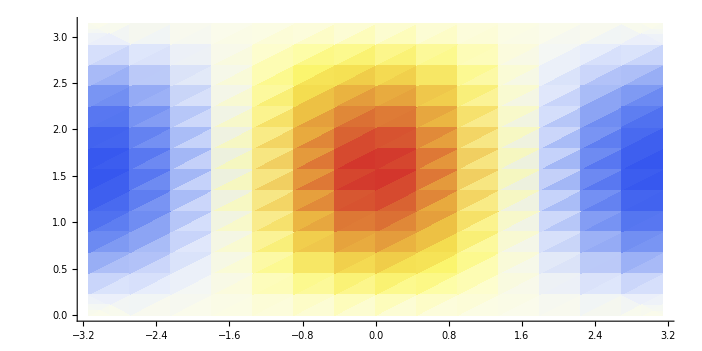

```mathematica
(*grid=With[{delta=Pi/18/2},Table[{lambda,phi},{phi,-Pi/2,Pi/2,delta},{lambda,-Pi,Pi,delta}]];*)
gr1=Graphics[{AbsoluteThickness[0.05],Line/@grid,Line/@Transpose[grid]},AspectRatio->1/2];
gr0=Flatten[{gr1[[1,2]][[Range[9]*4-1]],gr1[[1,3]][[Range[18]*4-3]]}]//Graphics[{AbsoluteThickness[0.2],#}]&;
(*gr2=Table[{Hue[t/Pi],Point[{t,t/2}]},{t,-Pi,Pi,1/100}]//Flatten//Graphics;*)
gr2=plt[1,-1];
gr=Show[{gr2},Axes->True]
```

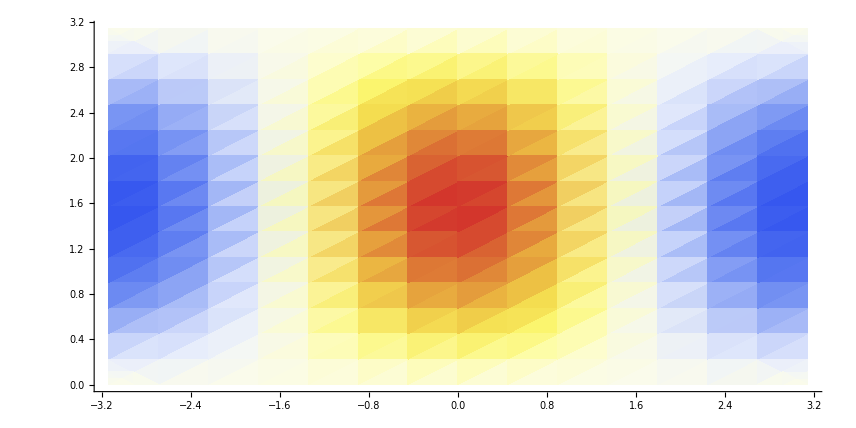

```mathematica
gr/.Line[pts_]:>Line[cart/@pts]/.Point[pts_]:>Point[cart[pts]]
```

## Drafts

```mathematica
Re[Exp[I 100]]
```

Cos[100]